# Symmetric KL divergence

## Setup

```mathematica
ClearAll["Global`*"]
```

```mathematica
lfi = d^2(a+b+2(a-b)sc)/(((s2^2 + c2^2) + 2s2 c2) * a b)
```

(d^2 (a+b+2 (a-b) sc))/(a b (c2^2+2 c2 s2+s2^2))

```mathematica
lfi0 ={a->a0, b->b0, sc->s0 c0, s2->s0^2, c2->c0^2}
lfi1 ={a->a1, b->b1, sc->s1 c1, s2->s1^2, c2->c1^2}
```

{a→a0,b→b0,sc→c0 s0,s2→s0^2,c2→c0^2}

{a→a1,b→b1,sc→c1 s1,s2→s1^2,c2→c1^2}

```mathematica
traces = {
trSig1Sig0->(a1 a0(s1^2 c0^2 + c1^2 s0^2) + a1 b0(s1^2 s0^2 + c1^2 c0^2) + b1 a0 (c1^2 c0^2 + s1^2 s0^2) + b1 b0(c1^2 s0^2 + s1^2 c0^2) - 2(a1-b1)(a0-b0)s1 c1 s0 c0)/(a1 b1(s1^4 + c1^4) + 2a1 b1 s1^2 c1^2),
trSig0Sig1->(a1 a0(s0^2 c1^2 + c0^2 s1^2) + a0 b1(s0^2 s1^2 + c0^2 c1^2) + b0 a1 (c0^2 c1^2 + s0^2 s1^2) + b1 b0(c0^2 s1^2 + s0^2 c1^2) - 2(a0-b0)(a1-b1)s0 c0 s1 c1)/(a0 b0(s0^4 + c0^4) + 2a0 b0 s0^2 c0^2)
}
```

{trSig1Sig0→1/(2 a1 b1 c1^2 s1^2+a1 b1 (c1^4+s1^4))(-2 (a0-b0) (a1-b1) c0 c1 s0 s1+a0 a1 (c1^2 s0^2+c0^2 s1^2)+b0 b1 (c1^2 s0^2+c0^2 s1^2)+a1 b0 (c0^2 c1^2+s0^2 s1^2)+a0 b1 (c0^2 c1^2+s0^2 s1^2)),trSig0Sig1→1/(2 a0 b0 c0^2 s0^2+a0 b0 (c0^4+s0^4))(-2 (a0-b0) (a1-b1) c0 c1 s0 s1+a0 a1 (c1^2 s0^2+c0^2 s1^2)+b0 b1 (c1^2 s0^2+c0^2 s1^2)+a1 b0 (c0^2 c1^2+s0^2 s1^2)+a0 b1 (c0^2 c1^2+s0^2 s1^2))}

```mathematica
trig = {s0->Sin[theta0],s1->Sin[theta1],c0->Cos[theta0],c1->Cos[theta1]}
```

{s0→Sin[theta0],s1→Sin[theta1],c0→Cos[theta0],c1→Cos[theta1]}

```mathematica
{s0->Sin[theta0-Pi/4],s1->Sin[theta1-Pi/4],c0->Cos[theta0-Pi/4],c1->Cos[theta1-Pi/4]}
```

{s0→-Sin[π/4-theta0],s1→-Sin[π/4-theta1],c0→Cos[π/4-theta0],c1→Cos[π/4-theta1]}

```mathematica
jeffreys = (1/2)(trSig1Sig0 + trSig0Sig1 + (lfi/.lfi0) + (lfi/.lfi1) - 2d)
```

1/2 (-2 d+(d^2 (a0+b0+2 (a0-b0) c0 s0))/(a0 b0 (c0^4+2 c0^2 s0^2+s0^4))+(d^2 (a1+b1+2 (a1-b1) c1 s1))/(a1 b1 (c1^4+2 c1^2 s1^2+s1^4))+trSig0Sig1+trSig1Sig0)

## Same eigenspectrum

```mathematica
jeffreys$eval = Simplify[jeffreys/.traces/.trig]
```

1/(4 a0 a1 b0 b1)(a0^2 a1 b0+a0 a1 b0^2+a0 a1^2 b1+a0^2 b0 b1+a1^2 b0 b1+a0 b0^2 b1+a0 a1 b1^2+a1 b0 b1^2-4 a0 a1 b0 b1 d+2 a0 a1 b0 d^2+2 a0 a1 b1 d^2+2 a0 b0 b1 d^2+2 a1 b0 b1 d^2-(a0-b0) (a1-b1) (a0 b0+a1 b1) Cos[2 (theta0-theta1)]+2 a1 (a0-b0) b1 d^2 Sin[2 theta0]+2 a0 a1 b0 d^2 Sin[2 theta1]-2 a0 b0 b1 d^2 Sin[2 theta1])

```mathematica
jeffreys$simplified = jeffreys$eval/.a1->a0/.b1->b0//Simplify
```

1/(2 a0 b0)(a0^2+2 a0 b0+b0^2-2 a0 b0 d+2 a0 d^2+2 b0 d^2-(a0-b0)^2 Cos[2 (theta0-theta1)]+(a0-b0) d^2 Sin[2 theta0]+a0 d^2 Sin[2 theta1]-b0 d^2 Sin[2 theta1])

```mathematica
Solve[Grad[jeffreys$simplified, {theta0, theta1}] == {0, 0}, {theta0, theta1}]
```

{{theta0→ConditionalExpression[1/2 (-π/2+2 π C[1]),C[1]∈ℤ],theta1→ConditionalExpression[1/2 (-π/2-2 π C[2]),C[2]∈ℤ]},{theta0→ConditionalExpression[1/2 (-π/2+2 π C[1]),C[1]∈ℤ],theta1→ConditionalExpression[1/2 (π/2-2 π C[2]),C[2]∈ℤ]},{theta0→ConditionalExpression[1/2 (π/2+2 π C[1]),C[1]∈ℤ],theta1→ConditionalExpression[1/2 (-π/2-2 π C[2]),C[2]∈ℤ]},{theta0→ConditionalExpression[1/2 (π/2+2 π C[1]),C[1]∈ℤ],theta1→ConditionalExpression[1/2 (π/2-2 π C[2]),C[2]∈ℤ]},{theta0→ConditionalExpression[1/2 (ArcTan[-(√(4 a0^2-8 a0 b0+4 b0^2-d^4))/(2 √(a0^2-2 a0 b0+b0^2)),d^2/(2 (a0-b0))]+2 π C[1]),C[1]∈ℤ],theta1→ConditionalExpression[1/2 (-ArcTan[(√(4 a0^2-8 a0 b0+4 b0^2-d^4))/(2 √((a0-b0)^2)),-d^2/(2 (a0-b0))]-2 π C[2]),C[2]∈ℤ]},{theta0→ConditionalExpression[1/2 (ArcTan[(√(4 a0^2-8 a0 b0+4 b0^2-d^4))/(2 √(a0^2-2 a0 b0+b0^2)),d^2/(2 (a0-b0))]+2 π C[1]),C[1]∈ℤ],theta1→ConditionalExpression[1/2 (-ArcTan[-(√(4 a0^2-8 a0 b0+4 b0^2-d^4))/(2 √((a0-b0)^2)),-d^2/(2 (a0-b0))]-2 π C[2]),C[2]∈ℤ]}}

## theta1 = theta0-Pi/2

```mathematica
Simplify[D[jeffreys$eval/.theta1->theta0-Pi/2, theta0]]
```

((a0 b0 b1-a1 b0 b1+a0 a1 (-b0+b1)) d^2 Cos[2 theta0])/(a0 a1 b0 b1)

```mathematica
Solve[D[jeffreys$eval/.theta1->theta0-Pi/2, theta0]==0, theta0]
```

{{theta0→ConditionalExpression[1/2 (-π/2+2 π C[1]),C[1]∈ℤ]},{theta0→ConditionalExpression[1/2 (π/2+2 π C[1]),C[1]∈ℤ]}}

```mathematica
hessian = D[jeffreys$eval/.theta1->theta0-Pi/2, {theta0, 2}]
```

(-8 a1 (a0-b0) b1 d^2 Sin[2 theta0]-8 a0 a1 b0 d^2 Sin[2 (-π/2+theta0)]+8 a0 b0 b1 d^2 Sin[2 (-π/2+theta0)])/(4 a0 a1 b0 b1)

## theta0 = -theta1

```mathematica
Simplify[D[jeffreys$simplified/.theta0->-theta1, theta1]]
```

(2 (a0-b0)^2 Sin[4 theta1])/(a0 b0)

```mathematica
Solve[D[jeffreys$simplified/.theta0->-theta1, theta1] == 0, theta1]
```

{{theta1→ConditionalExpression[π C[1],C[1]∈ℤ]},{theta1→ConditionalExpression[1/2 (-π/2+2 π C[1]),C[1]∈ℤ]},{theta1→ConditionalExpression[1/2 (π/2+2 π C[1]),C[1]∈ℤ]},{theta1→ConditionalExpression[1/2 (π+2 π C[1]),C[1]∈ℤ]}}

```mathematica
Simplify[Grad[jeffreys$simplified, {theta0, theta1}]]
```

{((a0-b0) (d^2 Cos[2 theta0]+(a0-b0) Sin[2 (theta0-theta1)]))/(a0 b0),((a0-b0) (d^2 Cos[2 theta1]+(-a0+b0) Sin[2 (theta0-theta1)]))/(a0 b0)}

```mathematica
hessian = D[jeffreys$simplified, {{theta0, theta1}, 2}]
```

{{(4 (a0-b0)^2 Cos[2 (theta0-theta1)]-4 (a0-b0) d^2 Sin[2 theta0])/(2 a0 b0),-(2 (a0-b0)^2 Cos[2 (theta0-theta1)])/(a0 b0)},{-(2 (a0-b0)^2 Cos[2 (theta0-theta1)])/(a0 b0),(4 (a0-b0)^2 Cos[2 (theta0-theta1)]-4 a0 d^2 Sin[2 theta1]+4 b0 d^2 Sin[2 theta1])/(2 a0 b0)}}

```mathematica
hessian$eigenvalues = Eigenvalues[hessian]
```

{1/4 (2/(a0^2 b0^3)-2/(a0^3 b0^2)) (4 a0^3 b0^2 Cos[2 theta0-2 theta1]-4 a0^2 b0^3 Cos[2 theta0-2 theta1]-√2 √(4 a0^6 b0^4-8 a0^5 b0^5+4 a0^4 b0^6+2 a0^4 b0^4 d^4-a0^4 b0^4 d^4 Cos[4 theta0]+4 a0^6 b0^4 Cos[4 theta0-4 theta1]-8 a0^5 b0^5 Cos[4 theta0-4 theta1]+4 a0^4 b0^6 Cos[4 theta0-4 theta1]-2 a0^4 b0^4 d^4 Cos[2 theta0-2 theta1]-a0^4 b0^4 d^4 Cos[4 theta1]+2 a0^4 b0^4 d^4 Cos[2 theta0+2 theta1])-2 a0^2 b0^2 d^2 Sin[2 theta0]-2 a0^2 b0^2 d^2 Sin[2 theta1]),1/4 (2/(a0^2 b0^3)-2/(a0^3 b0^2)) (4 a0^3 b0^2 Cos[2 theta0-2 theta1]-4 a0^2 b0^3 Cos[2 theta0-2 theta1]+√2 √(4 a0^6 b0^4-8 a0^5 b0^5+4 a0^4 b0^6+2 a0^4 b0^4 d^4-a0^4 b0^4 d^4 Cos[4 theta0]+4 a0^6 b0^4 Cos[4 theta0-4 theta1]-8 a0^5 b0^5 Cos[4 theta0-4 theta1]+4 a0^4 b0^6 Cos[4 theta0-4 theta1]-2 a0^4 b0^4 d^4 Cos[2 theta0-2 theta1]-a0^4 b0^4 d^4 Cos[4 theta1]+2 a0^4 b0^4 d^4 Cos[2 theta0+2 theta1])-2 a0^2 b0^2 d^2 Sin[2 theta0]-2 a0^2 b0^2 d^2 Sin[2 theta1])}

```mathematica
eig$perp=Simplify[hessian$eigenvalues/.theta0->Pi/4/.theta1->Pi/4,Assumptions->{a0>0, b0>0, d>0}]
```

{(2 (a0-b0) (a0-b0-d^2-Abs[a0-b0]))/(a0 b0),(2 (a0-b0) (a0-b0-d^2+Abs[a0-b0]))/(a0 b0)}

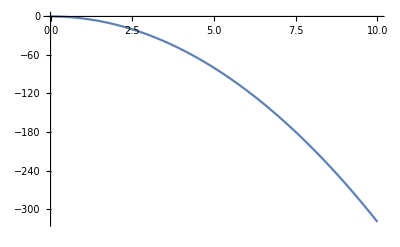

```mathematica
Plot[eig$perp[[1]]/.a0->2.5/.b0->0.5, {d,0,10}]
```

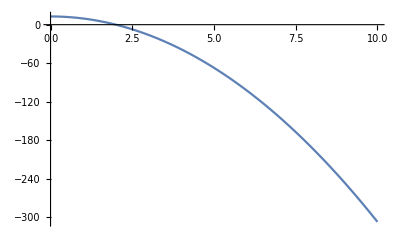

```mathematica
Plot[eig$perp[[2]]/.a0->2.5/.b0->0.5, {d,0,10}]
```

```mathematica
eig$perp[[2]]/.a0->2.5/.b0->0.5
```

3.2 (4.-d^2)

```mathematica
Simplify[Grad[jeffreys$eval, {theta0, theta1}]]
```

{((a0-b0) (2 a1 b1 d^2 Cos[2 theta0]+(a1-b1) (a0 b0+a1 b1) Sin[2 (theta0-theta1)]))/(2 a0 a1 b0 b1),(4 a0 a1 b0 d^2 Cos[2 theta1]-4 a0 b0 b1 d^2 Cos[2 theta1]-2 (a0-b0) (a1-b1) (a0 b0+a1 b1) Sin[2 (theta0-theta1)])/(4 a0 a1 b0 b1)}

```mathematica
hessian$total = D[jeffreys$eval, {{theta0, theta1}, 2}]
```

{{(4 (a0-b0) (a1-b1) (a0 b0+a1 b1) Cos[2 (theta0-theta1)]-8 a1 (a0-b0) b1 d^2 Sin[2 theta0])/(4 a0 a1 b0 b1),-((a0-b0) (a1-b1) (a0 b0+a1 b1) Cos[2 (theta0-theta1)])/(a0 a1 b0 b1)},{-((a0-b0) (a1-b1) (a0 b0+a1 b1) Cos[2 (theta0-theta1)])/(a0 a1 b0 b1),(4 (a0-b0) (a1-b1) (a0 b0+a1 b1) Cos[2 (theta0-theta1)]-8 a0 a1 b0 d^2 Sin[2 theta1]+8 a0 b0 b1 d^2 Sin[2 theta1])/(4 a0 a1 b0 b1)}}

```mathematica
hessian$total$eigenvalues = Eigenvalues[hessian$total]
```

{1/(2 a0^3 a1^3 b0^3 b1^3)(2 a0^4 a1^3 b0^3 b1^2 Cos[2 theta0-2 theta1]-2 a0^3 a1^3 b0^4 b1^2 Cos[2 theta0-2 theta1]+2 a0^3 a1^4 b0^2 b1^3 Cos[2 theta0-2 theta1]-2 a0^4 a1^2 b0^3 b1^3 Cos[2 theta0-2 theta1]-2 a0^2 a1^4 b0^3 b1^3 Cos[2 theta0-2 theta1]+2 a0^3 a1^2 b0^4 b1^3 Cos[2 theta0-2 theta1]-2 a0^3 a1^3 b0^2 b1^4 Cos[2 theta0-2 theta1]+2 a0^2 a1^3 b0^3 b1^4 Cos[2 theta0-2 theta1]-√2 √(a0^8 a1^6 b0^6 b1^4-2 a0^7 a1^6 b0^7 b1^4+a0^6 a1^6 b0^8 b1^4+2 a0^7 a1^7 b0^5 b1^5-2 a0^8 a1^5 b0^6 b1^5-4 a0^6 a1^7 b0^6 b1^5+4 a0^7 a1^5 b0^7 b1^5+2 a0^5 a1^7 b0^7 b1^5-2 a0^6 a1^5 b0^8 b1^5+a0^6 a1^8 b0^4 b1^6-4 a0^7 a1^6 b0^5 b1^6-2 a0^5 a1^8 b0^5 b1^6+a0^8 a1^4 b0^6 b1^6+8 a0^6 a1^6 b0^6 b1^6+a0^4 a1^8 b0^6 b1^6-2 a0^7 a1^4 b0^7 b1^6-4 a0^5 a1^6 b0^7 b1^6+a0^6 a1^4 b0^8 b1^6-2 a0^6 a1^7 b0^4 b1^7+2 a0^7 a1^5 b0^5 b1^7+4 a0^5 a1^7 b0^5 b1^7-4 a0^6 a1^5 b0^6 b1^7-2 a0^4 a1^7 b0^6 b1^7+2 a0^5 a1^5 b0^7 b1^7+a0^6 a1^6 b0^4 b1^8-2 a0^5 a1^6 b0^5 b1^8+a0^4 a1^6 b0^6 b1^8+a0^6 a1^6 b0^6 b1^4 d^4-2 a0^6 a1^5 b0^6 b1^5 d^4+a0^6 a1^6 b0^4 b1^6 d^4-2 a0^5 a1^6 b0^5 b1^6 d^4+a0^6 a1^4 b0^6 b1^6 d^4+a0^4 a1^6 b0^6 b1^6 d^4-a0^6 a1^6 b0^4 b1^6 d^4 Cos[4 theta0]+2 a0^5 a1^6 b0^5 b1^6 d^4 Cos[4 theta0]-a0^4 a1^6 b0^6 b1^6 d^4 Cos[4 theta0]+a0^8 a1^6 b0^6 b1^4 Cos[4 theta0-4 theta1]-2 a0^7 a1^6 b0^7 b1^4 Cos[4 theta0-4 theta1]+a0^6 a1^6 b0^8 b1^4 Cos[4 theta0-4 theta1]+2 a0^7 a1^7 b0^5 b1^5 Cos[4 theta0-4 theta1]-2 a0^8 a1^5 b0^6 b1^5 Cos[4 theta0-4 theta1]-4 a0^6 a1^7 b0^6 b1^5 Cos[4 theta0-4 theta1]+4 a0^7 a1^5 b0^7 b1^5 Cos[4 theta0-4 theta1]+2 a0^5 a1^7 b0^7 b1^5 Cos[4 theta0-4 theta1]-2 a0^6 a1^5 b0^8 b1^5 Cos[4 theta0-4 theta1]+a0^6 a1^8 b0^4 b1^6 Cos[4 theta0-4 theta1]-4 a0^7 a1^6 b0^5 b1^6 Cos[4 theta0-4 theta1]-2 a0^5 a1^8 b0^5 b1^6 Cos[4 theta0-4 theta1]+a0^8 a1^4 b0^6 b1^6 Cos[4 theta0-4 theta1]+8 a0^6 a1^6 b0^6 b1^6 Cos[4 theta0-4 theta1]+a0^4 a1^8 b0^6 b1^6 Cos[4 theta0-4 theta1]-2 a0^7 a1^4 b0^7 b1^6 Cos[4 theta0-4 theta1]-4 a0^5 a1^6 b0^7 b1^6 Cos[4 theta0-4 theta1]+a0^6 a1^4 b0^8 b1^6 Cos[4 theta0-4 theta1]-2 a0^6 a1^7 b0^4 b1^7 Cos[4 theta0-4 theta1]+2 a0^7 a1^5 b0^5 b1^7 Cos[4 theta0-4 theta1]+4 a0^5 a1^7 b0^5 b1^7 Cos[4 theta0-4 theta1]-4 a0^6 a1^5 b0^6 b1^7 Cos[4 theta0-4 theta1]-2 a0^4 a1^7 b0^6 b1^7 Cos[4 theta0-4 theta1]+2 a0^5 a1^5 b0^7 b1^7 Cos[4 theta0-4 theta1]+a0^6 a1^6 b0^4 b1^8 Cos[4 theta0-4 theta1]-2 a0^5 a1^6 b0^5 b1^8 Cos[4 theta0-4 theta1]+a0^4 a1^6 b0^6 b1^8 Cos[4 theta0-4 theta1]-2 a0^6 a1^6 b0^5 b1^5 d^4 Cos[2 theta0-2 theta1]+2 a0^5 a1^6 b0^6 b1^5 d^4 Cos[2 theta0-2 theta1]+2 a0^6 a1^5 b0^5 b1^6 d^4 Cos[2 theta0-2 theta1]-2 a0^5 a1^5 b0^6 b1^6 d^4 Cos[2 theta0-2 theta1]-a0^6 a1^6 b0^6 b1^4 d^4 Cos[4 theta1]+2 a0^6 a1^5 b0^6 b1^5 d^4 Cos[4 theta1]-a0^6 a1^4 b0^6 b1^6 d^4 Cos[4 theta1]+2 a0^6 a1^6 b0^5 b1^5 d^4 Cos[2 theta0+2 theta1]-2 a0^5 a1^6 b0^6 b1^5 d^4 Cos[2 theta0+2 theta1]-2 a0^6 a1^5 b0^5 b1^6 d^4 Cos[2 theta0+2 theta1]+2 a0^5 a1^5 b0^6 b1^6 d^4 Cos[2 theta0+2 theta1])-2 a0^3 a1^3 b0^2 b1^3 d^2 Sin[2 theta0]+2 a0^2 a1^3 b0^3 b1^3 d^2 Sin[2 theta0]-2 a0^3 a1^3 b0^3 b1^2 d^2 Sin[2 theta1]+2 a0^3 a1^2 b0^3 b1^3 d^2 Sin[2 theta1]),1/(2 a0^3 a1^3 b0^3 b1^3)(2 a0^4 a1^3 b0^3 b1^2 Cos[2 theta0-2 theta1]-2 a0^3 a1^3 b0^4 b1^2 Cos[2 theta0-2 theta1]+2 a0^3 a1^4 b0^2 b1^3 Cos[2 theta0-2 theta1]-2 a0^4 a1^2 b0^3 b1^3 Cos[2 theta0-2 theta1]-2 a0^2 a1^4 b0^3 b1^3 Cos[2 theta0-2 theta1]+2 a0^3 a1^2 b0^4 b1^3 Cos[2 theta0-2 theta1]-2 a0^3 a1^3 b0^2 b1^4 Cos[2 theta0-2 theta1]+2 a0^2 a1^3 b0^3 b1^4 Cos[2 theta0-2 theta1]+√2 √(a0^8 a1^6 b0^6 b1^4-2 a0^7 a1^6 b0^7 b1^4+a0^6 a1^6 b0^8 b1^4+2 a0^7 a1^7 b0^5 b1^5-2 a0^8 a1^5 b0^6 b1^5-4 a0^6 a1^7 b0^6 b1^5+4 a0^7 a1^5 b0^7 b1^5+2 a0^5 a1^7 b0^7 b1^5-2 a0^6 a1^5 b0^8 b1^5+a0^6 a1^8 b0^4 b1^6-4 a0^7 a1^6 b0^5 b1^6-2 a0^5 a1^8 b0^5 b1^6+a0^8 a1^4 b0^6 b1^6+8 a0^6 a1^6 b0^6 b1^6+a0^4 a1^8 b0^6 b1^6-2 a0^7 a1^4 b0^7 b1^6-4 a0^5 a1^6 b0^7 b1^6+a0^6 a1^4 b0^8 b1^6-2 a0^6 a1^7 b0^4 b1^7+2 a0^7 a1^5 b0^5 b1^7+4 a0^5 a1^7 b0^5 b1^7-4 a0^6 a1^5 b0^6 b1^7-2 a0^4 a1^7 b0^6 b1^7+2 a0^5 a1^5 b0^7 b1^7+a0^6 a1^6 b0^4 b1^8-2 a0^5 a1^6 b0^5 b1^8+a0^4 a1^6 b0^6 b1^8+a0^6 a1^6 b0^6 b1^4 d^4-2 a0^6 a1^5 b0^6 b1^5 d^4+a0^6 a1^6 b0^4 b1^6 d^4-2 a0^5 a1^6 b0^5 b1^6 d^4+a0^6 a1^4 b0^6 b1^6 d^4+a0^4 a1^6 b0^6 b1^6 d^4-a0^6 a1^6 b0^4 b1^6 d^4 Cos[4 theta0]+2 a0^5 a1^6 b0^5 b1^6 d^4 Cos[4 theta0]-a0^4 a1^6 b0^6 b1^6 d^4 Cos[4 theta0]+a0^8 a1^6 b0^6 b1^4 Cos[4 theta0-4 theta1]-2 a0^7 a1^6 b0^7 b1^4 Cos[4 theta0-4 theta1]+a0^6 a1^6 b0^8 b1^4 Cos[4 theta0-4 theta1]+2 a0^7 a1^7 b0^5 b1^5 Cos[4 theta0-4 theta1]-2 a0^8 a1^5 b0^6 b1^5 Cos[4 theta0-4 theta1]-4 a0^6 a1^7 b0^6 b1^5 Cos[4 theta0-4 theta1]+4 a0^7 a1^5 b0^7 b1^5 Cos[4 theta0-4 theta1]+2 a0^5 a1^7 b0^7 b1^5 Cos[4 theta0-4 theta1]-2 a0^6 a1^5 b0^8 b1^5 Cos[4 theta0-4 theta1]+a0^6 a1^8 b0^4 b1^6 Cos[4 theta0-4 theta1]-4 a0^7 a1^6 b0^5 b1^6 Cos[4 theta0-4 theta1]-2 a0^5 a1^8 b0^5 b1^6 Cos[4 theta0-4 theta1]+a0^8 a1^4 b0^6 b1^6 Cos[4 theta0-4 theta1]+8 a0^6 a1^6 b0^6 b1^6 Cos[4 theta0-4 theta1]+a0^4 a1^8 b0^6 b1^6 Cos[4 theta0-4 theta1]-2 a0^7 a1^4 b0^7 b1^6 Cos[4 theta0-4 theta1]-4 a0^5 a1^6 b0^7 b1^6 Cos[4 theta0-4 theta1]+a0^6 a1^4 b0^8 b1^6 Cos[4 theta0-4 theta1]-2 a0^6 a1^7 b0^4 b1^7 Cos[4 theta0-4 theta1]+2 a0^7 a1^5 b0^5 b1^7 Cos[4 theta0-4 theta1]+4 a0^5 a1^7 b0^5 b1^7 Cos[4 theta0-4 theta1]-4 a0^6 a1^5 b0^6 b1^7 Cos[4 theta0-4 theta1]-2 a0^4 a1^7 b0^6 b1^7 Cos[4 theta0-4 theta1]+2 a0^5 a1^5 b0^7 b1^7 Cos[4 theta0-4 theta1]+a0^6 a1^6 b0^4 b1^8 Cos[4 theta0-4 theta1]-2 a0^5 a1^6 b0^5 b1^8 Cos[4 theta0-4 theta1]+a0^4 a1^6 b0^6 b1^8 Cos[4 theta0-4 theta1]-2 a0^6 a1^6 b0^5 b1^5 d^4 Cos[2 theta0-2 theta1]+2 a0^5 a1^6 b0^6 b1^5 d^4 Cos[2 theta0-2 theta1]+2 a0^6 a1^5 b0^5 b1^6 d^4 Cos[2 theta0-2 theta1]-2 a0^5 a1^5 b0^6 b1^6 d^4 Cos[2 theta0-2 theta1]-a0^6 a1^6 b0^6 b1^4 d^4 Cos[4 theta1]+2 a0^6 a1^5 b0^6 b1^5 d^4 Cos[4 theta1]-a0^6 a1^4 b0^6 b1^6 d^4 Cos[4 theta1]+2 a0^6 a1^6 b0^5 b1^5 d^4 Cos[2 theta0+2 theta1]-2 a0^5 a1^6 b0^6 b1^5 d^4 Cos[2 theta0+2 theta1]-2 a0^6 a1^5 b0^5 b1^6 d^4 Cos[2 theta0+2 theta1]+2 a0^5 a1^5 b0^6 b1^6 d^4 Cos[2 theta0+2 theta1])-2 a0^3 a1^3 b0^2 b1^3 d^2 Sin[2 theta0]+2 a0^2 a1^3 b0^3 b1^3 d^2 Sin[2 theta0]-2 a0^3 a1^3 b0^3 b1^2 d^2 Sin[2 theta1]+2 a0^3 a1^2 b0^3 b1^3 d^2 Sin[2 theta1])}